# A w Phantom Transition at z_t<0.1 as a Resolution of the Hubble Tension - G. Alestas, L. Kazantzidis and L. Perivolaropoulos - Figures 1 and 2

## Section II - The Cosmological Comoving Distance in the LwPT Model

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,NMinimize::cvmit,NIntegrate::slwcon];
```

### Various Constants

```mathematica
(* Riess' measurement - See arxiv:1903.07603 *)
h0r=0.74;
(* Planck18 Values *)
h0c=0.674; 
om0=0.31;
```

### LwPT Model

#### Figure 1

-0.0868725/Log[1+zt]

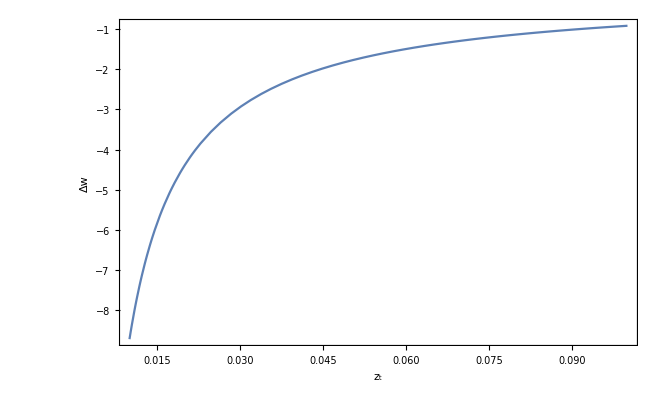

```mathematica
(* Relation between Δw and Subscript[z, t] where h=h0c, Subscript[ω, m]=om0 h0c^2 and Subscript[h, local]=h0r - Eq. (2.4) from our paper  *)
dw=(Log[h0c^2-om0 h0c^2]-Log[h0r^2-om0 h0c^2])/(3Log[(1+zt)])
(* Figure 1 - The equation of state shift Δw as a function of the transition redshift Subscript[z, t] *)
fig1=Plot[dw,{zt,0.01,0.1},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"z_t","Δw"},BaseStyle->{FontFamily->"Times",18},LabelStyle->Directive[Black,Large]]
```

```mathematica
Export["fig1.pdf",fig1,ImageResolution->1000,ImageSize->Full];
```

#### Figure 2

```mathematica
(* The H(z) deformation for Planck18/ΛCDM model - Eq. (2.1) from our paper *)
hlcdm[z_]:=h0c Sqrt[om0 (1+z)^3+(1-om0)]
(* The comoving distance Subscript[r, Λ] function for Planck18/ΛCDM model *)
rhlcdm[z_]:=NIntegrate[1/hlcdm[zp],{zp,0,z}];
(* The f(z)≡z/(r(z)) function for Planck18/ΛCDM model as a function of z*)
pl0=Plot[(rhlcdm[z]/z)^-1,{z,0,1},PlotStyle->{Black}];
```

```mathematica
(* The H(z) transition model - Eq. (2.5) from our paper *)
hdlcdm[z_,zt_]:=Piecewise[{{h0r Sqrt[om0 (1+z)^3+(1-om0)],z<zt},{h0c Sqrt[om0 (1+z)^3+(1-om0)],z>zt}}]
(* The comoving distance function for the H(z) transition model *)
rhdlcdm[z_,zt_]:=NIntegrate[1/hdlcdm[zp,zt],{zp,0,z}];
(* The f(z)≡z/(r(z)) function for the H(z) transition model as a function of z*)
pl1=Plot[(rhdlcdm[z,0.05]/z)^-1,{z,0,1},PlotStyle->{Red,DotDashed}];
```

```mathematica
(* The H(z) deformation for LwPT with Subscript[z, t]=0.1 *)
hwdlcdm[z_,zt_,dw_]:=Piecewise[{{h0c Sqrt[om0 (1+z)^3+(1-om0)((1+z)/(1+zt))^(3dw)],z<zt},{h0c Sqrt[om0 (1+z)^3+(1-om0)],z>zt}}]
(* The comoving distance function for the LwPT model with Subscript[z, t]=0.1 *)
rhwdlcdm[z_,zt_,dw_]:=NIntegrate[1/hwdlcdm[zp,zt,dw],{zp,0,z}];
(* The f(z)≡z/(r(z)) function for the LwPT model with Subscript[z, t]=0.1 as a function of z*)
pl2a=Plot[(rhwdlcdm[z,0.1,-0.9114716]/z)^-1,{z,0,1},PlotStyle->{Blue}];
```

```mathematica
(* The H(z) deformation for wCDM model - Eq. (2.6) from our paper *)
hwcdm[z_,w_]:= Sqrt[om0  h0c^2(1+z)^3+(h0r^2-om0 h0c^2)(1+z)^(3(1+w))];
(* The comoving distance function for wCDM model *)
rhwcdm[z_,w_]:=NIntegrate[1/hwcdm[zp,w],{zp,0,z}];
(* The f(z)≡z/(r(z)) function for wCDM model as a function of z*)
pl3=Plot[(rhwcdm[z,-1.2]/z)^-1,{z,0,1},PlotStyle->{Magenta,Thick,Dotted}];
```

```mathematica
(* The H(z) deformation for LwPT with Subscript[z, t]=0.05 *)
hwdlcdm[z_,zt_,w0_,w2_]:=Piecewise[{{h0c Sqrt[om0 (1+z)^3+(1-om0)((1+z)/(1+zt))^(3(1+w0))],z<zt},{h0c Sqrt[om0 (1+z)^3+(1-om0)(1+z)^(3(1+w2))],z>zt}}]
(* The comoving distance function for the LwPT model with Subscript[z, t]=0.05 *)
rhwdlcdm[z_,zt_,w0_,w2_]:=NIntegrate[1/hwdlcdm[zp,zt,w0,w2],{zp,0,z}];
(* The f(z)≡z/(r(z)) function for the LwPT model with Subscript[z, t]=0.05 as a function of z*)
pl2=Plot[(rhwdlcdm[z,0.05,-2.78,-1]/z)^-1,{z,0,1},PlotStyle->{Green,Dashed}];
```

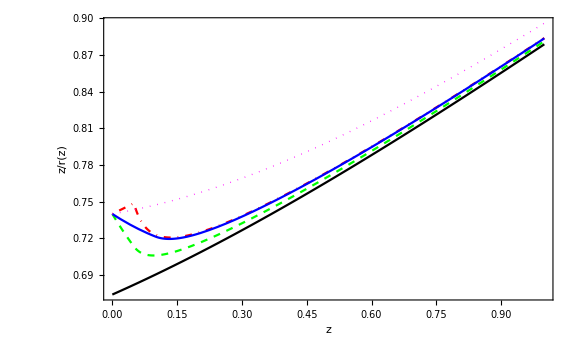

```mathematica
(* Figure 2 - The function f(z) as a function of z *)
fig2=Show[pl0,pl1,pl2,pl2a,pl3,Prolog->Inset[Framed[Column[{LineLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Black],Thick},{"Planck18/ΛCDM"}],LineLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Blue],Thick},{"LwPT (z_t=0.1)"}],LineLegend[{Directive[Dashed,Green],Thick},{"LwPT (z_t=0.05)"}],LineLegend[{Directive[DotDashed,Red],Thick},{"δH_0"}],LineLegend[{Directive[Dotted,Magenta],Thick},{"wCDM"}]}],RoundingRadius->5],Scaled[{0.85,0.27}],BaseStyle -> {FontFamily->"Times",10}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"z","z/r(z)"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None,LabelStyle->Directive[Black,Large]]
```

```mathematica
Export["fig2.pdf",fig2,ImageResolution->1000];
```